```mathematica
symbols[exp_]:=Union[Cases[exp,_Symbol,Infinity]]
Get["https://raw.githubusercontent.com/rhennigan/FactorExpression/master/FactorExpression.m"]
```

```mathematica
p[{x1_,y1_},{x2_,y2_},t_]:={(1-t)x1+t x2,(1-t)y1+t y2}
```

```mathematica
{t1,t2}=First[{t1,t2}/.Solve[(1-t1)*l1x1+t1*l1x2==(1-t2)*l2x1+t2*l2x2&&(1-t1)*l1y1+t1*l1y2==(1-t2)*l2y1+t2*l2y2,{t1,t2}]]
```

{-(-l1y1 l2x1+l1y1 l2x2+l1x1 l2y1-l2x2 l2y1-l1x1 l2y2+l2x1 l2y2)/(l1y1 l2x1-l1y2 l2x1-l1y1 l2x2+l1y2 l2x2-l1x1 l2y1+l1x2 l2y1+l1x1 l2y2-l1x2 l2y2),-(-l1x2 l1y1+l1x1 l1y2+l1y1 l2x1-l1y2 l2x1-l1x1 l2y1+l1x2 l2y1)/(-l1y1 l2x1+l1y2 l2x1+l1y1 l2x2-l1y2 l2x2+l1x1 l2y1-l1x2 l2y1-l1x1 l2y2+l1x2 l2y2)}

```mathematica
t1
```

-(-l1y1 l2x1+l1y1 l2x2+l1x1 l2y1-l2x2 l2y1-l1x1 l2y2+l2x1 l2y2)/(l1y1 l2x1-l1y2 l2x1-l1y1 l2x2+l1y2 l2x2-l1x1 l2y1+l1x2 l2y1+l1x1 l2y2-l1x2 l2y2)

```mathematica
{t1n,t1d}={Numerator[#],Denominator[#]}&@FullSimplify[t1,Element[symbols[t1],Reals]]
{t2n,t2d}={Numerator[#],Denominator[#]}&@FullSimplify[t2,Element[symbols[t2],Reals]]
```

{l1y1 (-l2x1+l2x2)-l2x2 l2y1+l1x1 (l2y1-l2y2)+l2x1 l2y2,-(l1y1-l1y2) (l2x1-l2x2)+(l1x1-l1x2) (l2y1-l2y2)}

{(l1y1-l1y2) l2x1+l1x1 (l1y2-l2y1)+l1x2 (-l1y1+l2y1),(l1y1-l1y2) (l2x1-l2x2)-(l1x1-l1x2) (l2y1-l2y2)}

```mathematica
t1n
```

l1y1 (-l2x1+l2x2)-l2x2 l2y1+l1x1 (l2y1-l2y2)+l2x1 l2y2

```mathematica
t1n
```

0

```mathematica
{{l1x1,l1y1},{l1x2,l1y2}}=RandomInteger[{1,3},{2,2}];
{{l2x1,l2y1},{l2x2,l2y2}}=RandomInteger[{1,3},{2,2}];

Quiet[results=Flatten[Table[{{{t1n,t1d,t1n/t1d},
{t2n,t2d,t2n/t2d}},
Graphics[{
Red, Arrow[{{l1x1,l1y1},{l1x2,l1y2}}],
Blue,Arrow[{{l2x1,l2y1},{l2x2,l2y2}}]
},PlotRange->{{0,4},{0,4}},Axes->True]},{l1x1,1,3},{l1y1,1,3},{l1x2,1,3},{l1y2,1,3}],3]];
```

```mathematica
TableForm[Select[results,Not[And@@(NumberQ/@Flatten[#⟦1⟧])]&]]
```

```mathematica
FactorExpression[{(l1x1-l1x2)*(l2y1-l2y2)-(l1y1-l1y2)*(l2x1-l2x2),((l2x1-l2x2)*(l1x1*l1y2-l1y1*l1x2)-(l1x1-l1x2)*(l2x1*l1y2-l1y1*l2x2)),((l1y1-l1y2)*(l1x1*l1y2-l1y1*l1x2)-(l1y1-l1y2)*(l2x1*l1y2-l1y1*l2x2))},"Language"->"C","Prefix"->"v","Comments"->False]
```

double v1 = -l2x2;
double v2 = -l1x2;
double v3 = -l1y2;
double v4 = l1y1 + v3;
double v5 = l1x1 + v2;
double v6 = l2x1 + v1;
double v7 = -v4;
double v8 = l1y2*l2x1;
double v9 = l1x1*l1y2;
double v10 = l1y1*v1;
double v11 = v10 + v8;
double v12 = l1y1*v2;
double v13 = v12 + v9;
return List((l2y1 - l2y2)*v5 + v6*v7,-(v11*v5) + v13*v6,v13*v4 + v11*v7);

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

```mathematica
exp=VectorAngle[{x2-x1,y2-y1},{x4-x3,y4-y3}];
FullSimplify[exp,Element[symbols[exp],Reals]]
```

ArcCos[((x1-x2) (x3-x4)+(y1-y2) (y3-y4))/(√(((x1-x2)^2+(y1-y2)^2) ((x3-x4)^2+(y3-y4)^2)))]

```mathematica
With[
{x1=0,y1=0,z1=0,x2=1,y2=1,z2=1},
Det[{{x2-x1,y2-y1,z2-z1},{x4-x3,y4-y3,z4-z3},{1,1,1}}]
]
```

0

```mathematica
{x1,y1,z1},{x2,y2,z2}
{x3,y3,z3},{x4,y4,z4}
```

```mathematica
Solve[{x2-x1,y2-y1,z2-z1}.{x0,y0,z0}==0&&{x4-x3,y4-y3,z4-z3}.{x0,y0,z0}==0,{x0,y0,z0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y0→-(x0 (x3 z1-x4 z1-x3 z2+x4 z2-x1 z3+x2 z3+x1 z4-x2 z4))/(y3 z1-y4 z1-y3 z2+y4 z2-y1 z3+y2 z3+y1 z4-y2 z4),z0→-(x0 (-x3 y1+x4 y1+x3 y2-x4 y2+x1 y3-x2 y3-x1 y4+x2 y4))/(y3 z1-y4 z1-y3 z2+y4 z2-y1 z3+y2 z3+y1 z4-y2 z4)}}

```mathematica
exp=VectorAngle[{x2-x1,y2-y1,z2-z1},{x4-x3,y4-y3,z4-z3}]
```

ArcCos[((-x1+x2) (-Conjugate[x3]+Conjugate[x4])+(-y1+y2) (-Conjugate[y3]+Conjugate[y4])+(-z1+z2) (-Conjugate[z3]+Conjugate[z4]))/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))]

```mathematica
FullSimplify[exp,Element[symbols[exp],Reals]]
```

ArcCos[((x1-x2) (x3-x4)+(y1-y2) (y3-y4)+(z1-z2) (z3-z4))/(√(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) ((x3-x4)^2+(y3-y4)^2+(z3-z4)^2)))]

```mathematica
InputForm[ArcCos[((x1-x2) (x3-x4)+(y1-y2) (y3-y4)+(z1-z2) (z3-z4))/(√(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) ((x3-x4)^2+(y3-y4)^2+(z3-z4)^2)))]]
```

ArcCos[((x1 - x2)*(x3 - x4) + (y1 - y2)*(y3 - y4) + (z1 - z2)*(z3 - z4))/
  Sqrt[((x1 - x2)^2 + (y1 - y2)^2 + (z1 - z2)^2)*((x3 - x4)^2 + (y3 - y4)^2 + (z3 - z4)^2)]]

```mathematica
exp=VectorAngle[{ux,uy,uz},{vx,vy,vz}];
FullSimplify[exp,Element[symbols[exp],Reals]]
```

ArcCos[(ux vx+uy vy+uz vz)/(√((ux^2+uy^2+uz^2) (vx^2+vy^2+vz^2)))]

```mathematica
VectorAngle[{1,0,0},{-1,0,0}]
```

π

```mathematica
Solve[(1-t1)*x1+t1*x2==(1-t2)*x3+t2*x4&&
(1-t1)*y1+t1*y2==(1-t2)*y3+t2*y4&&
(1-t1)*z1+t1*z2==(1-t2)*z3+t2*z4]
```

{{x4→(x1-t1 x1+t1 x2-x3+t2 x3)/t2,y4→(y1-t1 y1+t1 y2-y3+t2 y3)/t2,z4→(z1-t1 z1+t1 z2-z3+t2 z3)/t2},{t2→0,x2→(-x1+t1 x1+x3)/t1,y2→(-y1+t1 y1+y3)/t1,z2→(-z1+t1 z1+z3)/t1},{t1→0,t2→0,x3→x1,y3→y1,z3→z1}}

```mathematica
p1={x1,y1,z1};
p2={x2,y2,z2};
p3={x3,y3,z3};
p4={x4,y4,z4};
p={x,y,z};
```

```mathematica
c=Cross[p2-p1,p4-p3]
```

{-y3 z1+y4 z1+y3 z2-y4 z2+y1 z3-y2 z3-y1 z4+y2 z4,x3 z1-x4 z1-x3 z2+x4 z2-x1 z3+x2 z3+x1 z4-x2 z4,-x3 y1+x4 y1+x3 y2-x4 y2+x1 y3-x2 y3-x1 y4+x2 y4}

```mathematica
exp=Norm[c]
```

√(Abs[-x3 y1+x4 y1+x3 y2-x4 y2+x1 y3-x2 y3-x1 y4+x2 y4]^2+Abs[x3 z1-x4 z1-x3 z2+x4 z2-x1 z3+x2 z3+x1 z4-x2 z4]^2+Abs[-y3 z1+y4 z1+y3 z2-y4 z2+y1 z3-y2 z3-y1 z4+y2 z4]^2)

```mathematica
FullSimplify[exp,Element[symbols[exp],Reals]]
```

√(((x3-x4) (y1-y2)-(x1-x2) (y3-y4))^2+((x3-x4) (z1-z2)-(x1-x2) (z3-z4))^2+((y3-y4) (z1-z2)-(y1-y2) (z3-z4))^2)

```mathematica
InputForm[√(((x3-x4) (y1-y2)-(x1-x2) (y3-y4))^2+((x3-x4) (z1-z2)-(x1-x2) (z3-z4))^2+((y3-y4) (z1-z2)-(y1-y2) (z3-z4))^2)]
```

Sqrt[((x3 - x4)*(y1 - y2) - (x1 - x2)*(y3 - y4))^2 + ((x3 - x4)*(z1 - z2) - (x1 - x2)*(z3 - z4))^2 + 
  ((y3 - y4)*(z1 - z2) - (y1 - y2)*(z3 - z4))^2]

```mathematica
f[{p1_,p2_},{p3_,p4_}]:=Module[{},
((x3-x4) (y1-y2)-(x1-x2) (y3-y4))^2+((x3-x4) (z1-z2)-(x1-x2) (z3-z4))^2+((y3-y4) (z1-z2)-(y1-y2) (z3-z4))^2
]
```

```mathematica
SolveAlways[p==p1+(p2-p1)s&&p==p3+(p4-p3)t,{s,t}]
```

{{x→x4,x1→x4,x2→x4,x3→x4,y→y4,y1→y4,y2→y4,y3→y4,z→z4,z1→z4,z2→z4,z3→z4}}

```mathematica
a=p2-p1;
b=p4-p3;
c=p3-p1;
```

```mathematica
v=Normalize[a]×Normalize[b]
```

{-(y3 z1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(y4 z1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(y3 z2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(y4 z2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(y1 z3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(y2 z3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(y1 z4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(y2 z4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2)),(x3 z1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x4 z1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x3 z2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x4 z2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x1 z3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x2 z3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x1 z4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x2 z4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2)),-(x3 y1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x4 y1)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x3 y2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x4 y2)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x1 y3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x2 y3)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))-(x1 y4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))+(x2 y4)/(√(Abs[-x1+x2]^2+Abs[-y1+y2]^2+Abs[-z1+z2]^2) √(Abs[-x3+x4]^2+Abs[-y3+y4]^2+Abs[-z3+z4]^2))}

```mathematica
InputForm@Det[({{{{ux, uy, uz}, {□, □, □}, {□, □, □}}□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}})]
```

-(uz*vy*wx) + uy*vz*wx + uz*vx*wy - ux*vz*wy - uy*vx*wz + ux*vy*wz

```mathematica
Det[({{ux, uy, uz, uw}, {vx, vy, vz, vw}, {wx, wy, wz, ww}, {xx, xy, xz, xw}})]/.{
ux->"u.x",uy->"u.y",uz->"u.z",uw->"u.w",
vx->"v.x",vy->"v.y",vz->"v.z",vw->"v.w",
wx->"w.x",wy->"w.y",wz->"w.z",ww->"w.w",
xx->"x.x",xy->"x.y",xz->"x.z",xw->"x.w"}
```

-u.z v.y w.x x.w+u.y v.z w.x x.w+u.z v.x w.y x.w-u.x v.z w.y x.w-u.y v.x w.z x.w+u.x v.y w.z x.w+u.z v.y w.w x.x-u.y v.z w.w x.x-u.z v.w w.y x.x+u.w v.z w.y x.x+u.y v.w w.z x.x-u.w v.y w.z x.x-u.z v.x w.w x.y+u.x v.z w.w x.y+u.z v.w w.x x.y-u.w v.z w.x x.y-u.x v.w w.z x.y+u.w v.x w.z x.y+u.y v.x w.w x.z-u.x v.y w.w x.z-u.y v.w w.x x.z+u.w v.y w.x x.z+u.x v.w w.y x.z-u.w v.x w.y x.z

```mathematica
24/4
```

6

```mathematica
With[{exp=Det[({{ux, uy, uz, uw}, {vx, vy, vz, vw}, {wx, wy, wz, ww}, {xx, xy, xz, xw}})]},FullSimplify[exp,Element[symbols[exp],Reals]]]
```

-uz vy wx+uy vz wx+uz vx wy-ux vz wy-uy vx wz+ux vy wz

```mathematica
Cross[{ux,uy,uz},{vx,vy,vz}]//InputForm
```

{-(uz*vy) + uy*vz, uz*vx - ux*vz, -(uy*vx) + ux*vy}

```mathematica
ClearAll[v]
```

```mathematica
Det[{{e1, e2, e3, e4}, {u.x, u.y, u.z, u.w}, {v.x, v.y, v.z, v.w}, {w.x, w.y, w.z, w.w}}]/.{
e1->{1,0,0,0},
e2->{0,1,0,0},
e3->{0,0,1,0},
e4->{0,0,0,1}
}//InputForm
```

{-(u . z*v . y*w . w) + u . y*v . z*w . w + u . z*v . w*w . y - u . w*v . z*w . y - u . y*v . w*w . z + 
  u . w*v . y*w . z, u . z*v . x*w . w - u . x*v . z*w . w - u . z*v . w*w . x + u . w*v . z*w . x + u . x*v . w*w . z - 
  u . w*v . x*w . z, -(u . y*v . x*w . w) + u . x*v . y*w . w + u . y*v . w*w . x - u . w*v . y*w . x - 
  u . x*v . w*w . y + u . w*v . x*w . y, u . z*v . y*w . x - u . y*v . z*w . x - u . z*v . x*w . y + u . x*v . z*w . y + 
  u . y*v . x*w . z - u . x*v . y*w . z}

```mathematica
v={a1,a2,a3}×{b1,b2,b3}
```

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

```mathematica
FullSimplify[Norm[v],Assumptions->{Norm[{a1,a2,a3}]==1,Norm[{b1,b2,b3}]==1,Element[symbols[v],Reals]}]
```

√((a2 b1-a1 b2)^2+(a3 b1-a1 b3)^2+(a3 b2-a2 b3)^2)

```mathematica
Module[{a1,a2,a3,b1,b2,b3,a,b},
{a1,a2,a3,b1,b2,b3}=RandomReal[{-5,5},6];
a=Normalize[{a1,a2,a3}];
b=Normalize[{b1,b2,b3}];
Norm[a×b]]
```

0.970251

```mathematica
r=100.0;
```

```mathematica
With[{n=10},Table[Cos[π/n],{t,0,2Pi,(2Pi)/n}]]
```

{95.1057,95.1057,95.1057,95.1057,95.1057,95.1057,95.1057,95.1057,95.1057,95.1057,95.1057}

```mathematica
ClearAll[r]
```

```mathematica
exp=Norm[Mean[{r{Cos[t],Sin[t]},r{Cos[t+(2Pi)/n],Sin[t+(2Pi)/n]}}]]
```

√(1/4 Abs[r Cos[t]+r Cos[(2 π)/n+t]]^2+1/4 Abs[r Sin[t]+r Sin[(2 π)/n+t]]^2)

```mathematica
FullSimplify[exp,Assumptions->{Element[{t,r,n},Reals],r>0,n>3}]
```

r Cos[π/n]

```mathematica
255List@@MyColors[3]
```

{102,203,57}

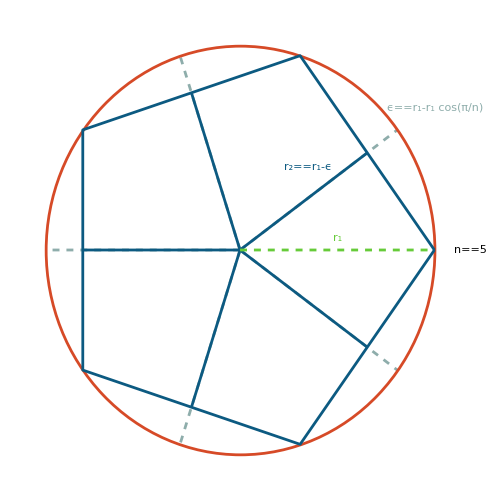

```mathematica
pts=With[{n=5},Table[{Cos[t],Sin[t]},{t,0,2Pi,(2Pi)/n}]];
p=Partition[pts,2,1];
img=Graphics[{
Dashed,AbsoluteThickness[2],MyColors[4],
Line[{{0,0},Normalize@Mean[#]}]&/@p,
Dashing[None],AbsoluteThickness[2],MyColors[2],
Circle[{0,0},1],
AbsoluteThickness[2],MyColors[1],
Line[pts],
Line[{{0,0},Mean[#]}]&/@p,
Black,Style[Text[n==5,{1.1,0},{Left,Center}],{Bold,16}],
Dashed,MyColors[3],Line[{{0,0},{1,0}}],
Style[Text[Subscript[r, 1],{0.5,.035},{Center,Bottom}],{12}],
MyColors[1],Style[Text[Subscript[r, 2]==Subscript[r, 1]-ϵ,RotationMatrix[.05].Mean[First[p]]*.75,{Right,Bottom}],{12}],
MyColors[4],Style[Text[ϵ==Subscript[r, 1]-Subscript[r, 1] Cos[π/n],RotationMatrix[.1].Mean[First[p]]*1.25,{Left,Bottom}],{12}]
},ImageSize->{500,500}]
```

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\final\\3\\r2.png",ImageCrop[Rasterize[Graphics[Style[Text[Subscript[r, 2]==Subscript[r, 1]-ϵ,RotationMatrix[.05].Mean[First[p]]*.75,{Right,Bottom}],{12}],ImageSize->2000],RasterSize->2000]]]
```

E:\GDrive\Classes\Computer Graphics\final\3\r2.png

```mathematica
ImageDimensions[%]
```

{51,10}

```mathematica
ExportString[img,"SVG"]
```

```mathematica
ClearAll[r,n]
```

```mathematica
exp=r-r Cos[π/n]
FullSimplify[exp,Assumptions->{Element[{t,r,n},Reals],r>0,n>3}]
```

r-r Cos[π/n]

r-r Cos[π/n]

```mathematica
ClearAll[α,β,γ,θ,a,b,c]
```

```mathematica
Solve[θ+2α==π,α]
```

{{α→(π-θ)/2}}

```mathematica
FullSimplify[(π-θ)/2+θ/2+π/2,0≤θ≤Pi]
```

π

```mathematica
Solve[a/Sin[π/2-θ]==r/Sin[π/2],a]
```

{{a→r Cos[θ]}}

```mathematica
Solve[α+β+γ==Pi,α]
```

{{α→(π-θ)/2}}

```mathematica
With[{r=100,θ=0},r Sin[(π-θ)/2]]
```

100

```mathematica
α=(π-θ)/2
β=θ/2
γ=π/2
c=r
Solve[a/Sin[α]==c/Sin[γ],a]
Solve[a^2==b^2+c^2-2 b c Cos[α],a]
```

(π-θ)/2

θ/2

π/2

r

{{a→r Sin[(π-θ)/2]}}

{{a→-√(b^2+r^2-2 b r Cos[(π-θ)/2])},{a→√(b^2+r^2-2 b r Cos[(π-θ)/2])}}

```mathematica
With[{n=5},(Pi-(2Pi)/n)/2]
```

(3 π)/10

```mathematica
%//N
```

0.942478

```mathematica
Clear[a,b,c]
```

```mathematica
√(a^2+b^2-2a b Cos[θ])
```

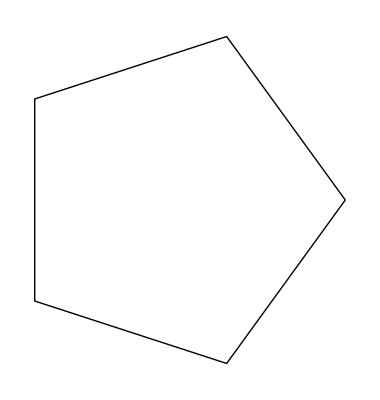

```mathematica
Graphics[Line@With[{n=5},Table[{Cos[t],Sin[t]},{t,0,2Pi,(2Pi)/n}]]]
```